# Kerr Geodesics

The KerrGeodesics package provides functions for computing quantities related to bound timelike geodesic orbits in Kerr spacetime. Before using the functions, first load the package

```mathematica
<<KerrGeodesics`
```

### Constants of motion and orbital frequencies

```mathematica
KerrGeoELQ[0.9`20,10,0.5`20,π/3]
```

```mathematica
KerrGeoFreqs[0.9`20,10,0.5`20,π/3]
```

Some cases can be evaluated analytically, e.g.,

```mathematica
KerrGeoELQ[0,p,e,0](*Schwarzschild orbit*)
```

```mathematica
KerrGeoELQ[a,p,0,π/2](*Polar, spherical orbit*)
```

### ISCO, separatrix, photon sphere, IBSO and ISSO

Radius of the ISCO for prograde and retrograde orbits for given a

```mathematica
KerrGeoISCO[0.99`20]
KerrGeoISCO[0.99`20,Orbit->"Retrograde"]
```

Find the value of p at the separatrix for generic orbits given (a,e,θinc)

```mathematica
KerrGeoSeparatrix[0.9,0.5,π/3]
```

4.34226

Radius of the photon sphere for a=M

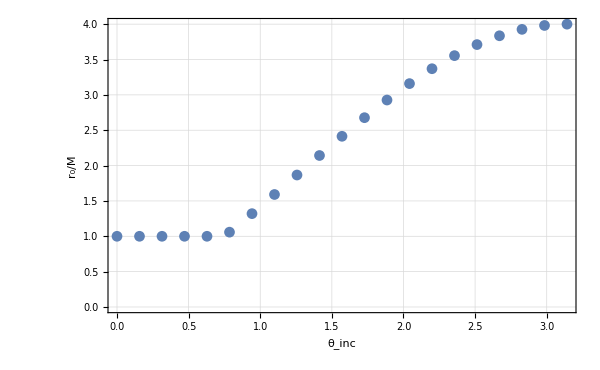

```mathematica
Table[{θ,KerrGeoPhotonSphereRadius[1,θ]},{θ,0,π,π/20.}];
ListPlot[%,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{"θ_inc","r_0/M"},BaseStyle->20]
```

Note the Boyer-Lindquist radius reduces to the r_0/M = 1 for low inclination values

Some values (particularly for a={0,M}) give exact results

```mathematica
KerrGeoPhotonSphereRadius[1,#]&/@{π/4,π/2,3π/4}
```

Compute the radius of the photon sphere, inner-most bound/stable orbits (IBSO and ISSO). Note we always have r_ph≤ r_IBSO≤ r_ISSO

```mathematica
KerrGeoPhotonSphereRadius[0.9,π/3]
KerrGeoIBSO[0.9,π/3]
KerrGeoISSO[0.9,π/3]
```

Plot the photo sphere radius, IBSO and ISSO for given black hole spin

```mathematica
PlotSpherical[a_]:=Block[{rph,rmb,rms,n=30},
rph=Table[{KerrGeoPhotonSphereRadius[a,θ],180 θ/π},{θ,0,π,π/n}];
rmb=Table[{KerrGeoIBSO[a,θ],180 θ/π},{θ,0,π,π/n}];
rms=Table[{KerrGeoISSO[a,θ],180 θ/π},{θ,0,π,π/n}];
Show[
Plot[180,{r,rmb[[-1,1]],rms[[-1,1]]},PlotStyle->None,Filling->Axis,FillingStyle->LightRed,PlotTheme->"Detailed",Frame->True,ImageSize->800,Axes->False,BaseStyle->20,FrameLabel->{"r/M","θ_inc"}],
Plot[180,{r,rms[[-1,1]],10},PlotStyle->None,Filling->Axis,FillingStyle->LightBlue],
ListPlot[{rph,rmb,rms,7},Filling->{2->{Axis,LightRed},3->{Axis,LightBlue}},Joined->True,PlotStyle->{Green,Red,Blue}],
PlotRange->All
]
]
```

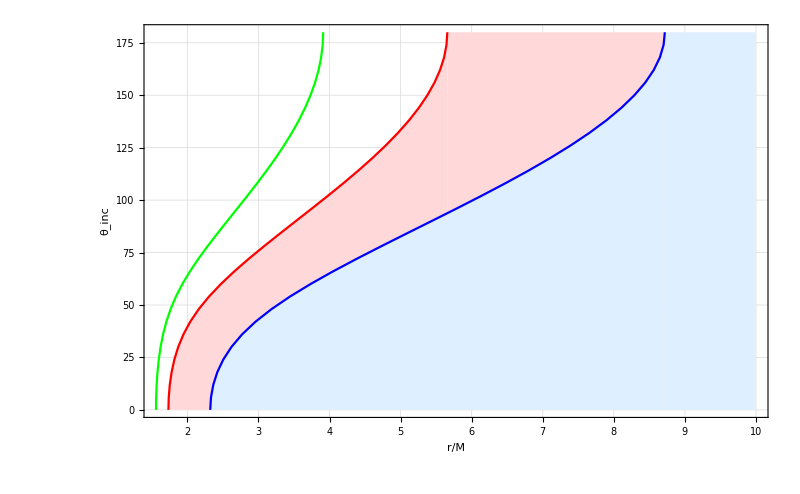

```mathematica
PlotSpherical[0.9]
```

In the above plot the blue curve is the ISSO, the red the IBSO and the green the photon sphere

### Visualize the orbit

```mathematica
KerrEqProgradePlot[a_,p_,e_,χmax_]:=Block[{orbit,rmax,t,r,θ,ϕ,stable},
stable=KerrGeoStableOrbitQ[a,p,e,0];
If[stable==True,
orbit=KerrGeoOrbit[a,p,e,0];
{t,r,θ,ϕ}=orbit["Interpolation"];(*The interpolated version is faster to evaluate*)
];
rmax=p/(1-e)+1;
Show[
If[stable==True,
ParametricPlot[{r[χ]Cos[ϕ[χ]],r[χ]Sin[ϕ[χ]]},{χ,0,χmax},ImageSize->600,PlotPoints->100,Frame->True,Axes->False],
Graphics[Text[Style["No stable orbit for those parameters",FontSize->20],{0,rmax-1}]]
],
Graphics[Disk[{0,0},1+Sqrt[1-a^2]]],PlotRange->{{-rmax,rmax},{-rmax,rmax}}
]
];
```

```mathematica
KerrEqProgradePlot[0.9,4,0.7,10π]
```

Use the following command to Manipulate the orbital parameters

```mathematica
(*
Manipulate[KerrEqProgradePlot[a,p,e,χmax],{{a,0.9},0,0.99},{{p,7.1},1,30},{{e,0.7},0,0.9},{{χmax,10π},2π,20π}]
*)
```